## MICA: Measurement, Instrumentation, Control & Analysis

## Newton’s Method

#### Ariel Mobius, MIT, 19 March 2026

Portrait of Isaac Newton (1642-1727). This is a copy of a painting by Sir Godfrey Kneller (1689).

#### Revisions

2023		Nov	13	Created from earlier Mathcad notebook
		Nov	14	Added tabular display of estimates and errors
2025		Apr	 3	Updated
		Nov	24	Updated
2026		Mar	19	Updated

#### Objectives

To introduce Newton’s  iterative method to find a root of a function.

#### Keywords

Newton’s Method, Iterative Algorithms, Roots, Golden Ratio

#### Background

The roots of a function, g(x), are simply the x values when g(x)=0 (i.e. the points at which a function
crosses or touches the x-axis). The roots of second-, third- and fourth-order polynomials (i.e. a quadratic, cubic and quartic polynomials) may be found using explicit formulas. (mathematicians spent considerable time searching for such formulas for 5th and higher order polynomials until the Norwegian mathematician Neils Abel proved that no such formulas were possible).

#### Second-Order Polynomials

Second-order polynomials are of the form:

```mathematica
g[x_,a_,b_,c_]:=a x^2+b x+c;
```

The formulas for the 2 roots are

```mathematica
xLower[a_,b_,c_]:=(-b-√(b^2-4 a c))/(2 a)
```

```mathematica
xHigher[a_,b_,c_]:=(-b+√(b^2-4 a c))/(2 a)
```

For example the function

```mathematica
g[x_]:=x^2-x-1
```

has roots

```mathematica
xLo=xLower[1,-1,-1]
```

1/2 (1-√5)

```mathematica
N[xLo]
```

-0.618034

and

```mathematica
xHi=xHigher[1,-1,-1]
```

1/2 (1+√5)

```mathematica
N[xHi]
```

1.61803

The higher root (positive root) of this function is called the Golden Ratio.

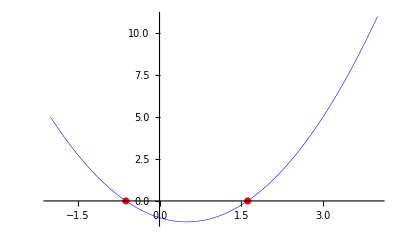

```mathematica
Show[
Plot[g[x],{x,-2,4},PlotRange->All,PlotStyle->{Thickness[0.001],Blue}],
ListPlot[{{xLo,0},{xHi,0}},PlotStyle->Red]]
```

#### Newton’s Method

But what do we do when we do not know the formulas for the roots?
A number of methods exist to find roots when explicit formulas are not available. The most famous of these methods is called Newton’s method (or the Newton-Raphson method) developed by Issac Newton in the mid 1600s. 
The idea behind this method is to start with an initial guess which is close to the desired root.

In the example above lets try to find the second root, xHi (the Golden Ratio).
We will call our initial guess x0 and set

```mathematica
x0=2.0;
```

We next find the slope of g[x] at the point (x0,g[x0]).
We can get this by differentiation

```mathematica
g'[x]
```

-1+2 x

Newton’s method specifies the next “guess” as

```mathematica
x1=x0-g[x0]/g'[x0]
```

1.66667

Newton’s method specifies the next “guess” as

```mathematica
x2=x1-g[x1]/g'[x1]
```

1.61905

```mathematica
x2
```

1.61905

This is close to the true value of the Golden Ratio

```mathematica
{x2,N[1/2 (1+√5),6]}
```

{1.61905,1.61803}

We can plot the progress in the estimates towards the true value of the Golden Ratio (shown with the open circle):

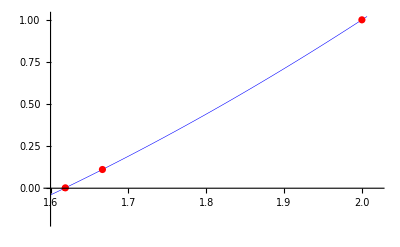

```mathematica
Show[
Plot[g[x],{x,1.6,2.2},PlotRange->{{1.6,2.02},{-0.2,1.02}},PlotStyle->{Thickness[0.001],Blue}],
ListPlot[{{x0,x1,x2},{g[x0],g[x1],g[x2]}}ᵀ,PlotStyle->Red],
ListPlot[{{1/2 (1+√5),0}},PlotStyle->Red,PlotMarkers->"OpenMarkers"]]
```

Newton’s method specifies the next “guesses” as

```mathematica
x3=x2-g[x2]/g'[x2];
x4=x3-g[x3]/g'[x3];
x5=x4-g[x4]/g'[x4];
x6=x5-g[x5]/g'[x5];
```

Lets look at the various estimates and their error:

```mathematica
dif=NumberForm[Column[{g[x0]/g'[x0],g[x1]/g'[x1],g[x2]/g'[x2],g[x3]/g'[x3],g[x4]/g'[x4],g[x5]/g'[x5],g[x6]/g'[x6]}],20,ExponentFunction->(Null&)];
est=NumberForm[Column[{x0,x1,x2,x3,x4,x5,x6}],20,ExponentFunction->(Null&)];
err=NumberForm[Column[{x0,x1,x2,x3,x4,x5,x6}-1/2 (1.0+√5)],20,ExponentFunction->(Null&)];
TableForm[{est,dif,err},TableDirections->Row,TableHeadings->{{"Estimate","g[xi]/g'[xi]","Error"},None}]
```

Estimate | g[xi]/g'[xi] | Error
2.
1.666666666666667
1.619047619047619
1.618034447821682
1.618033988749989
1.618033988749895
1.618033988749895 | 0.3333333333333333
0.04761904761904773
0.001013171225937151
0.0000004590716929011784
0.0000000000000941376950911287
0.
0. | 0.3819660112501051
0.04863267791677184
0.001013630297724166
0.0000004590717870289751
0.0000000000000941469124882133
0.
0.

Clearly Newton’s method has converged to the correct value of the Golden Ratio in a few iterations.

We can look at the fast convergence in the following plot:

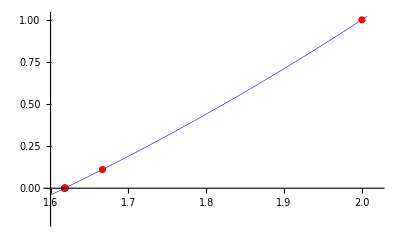

```mathematica
Show[
Plot[g[x],{x,1.6,2.2},PlotRange->{{1.6,2.02},{-0.2,1.02}},PlotStyle->{Thickness[0.001],Blue}],
ListPlot[{{x0,x1,x2,x3,x4,x5,x6},{g[x0],g[x1],g[x2],g[x3],g[x4],g[x5],g[x6]}}ᵀ,PlotStyle->Red]]
```

The convergence is so fast that we can only see the first few estimates as different from the exact value on this plot.

#### Find Pi

We can use Newton’s Method to estimate π by observing that Sin[x] becomes 0 when x = π. In other words the first positive root of Sin[x] is π. Lets check:

```mathematica
Sin[π]
```

0

So we set up the required function (Sin[x] and its derivative:

```mathematica
g[x_]:=Sin[x]
```

```mathematica
g'[x]
```

Cos[x]

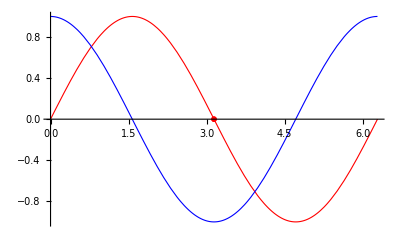

```mathematica
Show[
Plot[{g[x],g'[x]},{x,0,2π},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}}],
ListPlot[{{π,0}},PlotStyle->Red,PlotMarkers->"OpenMarkers"]]
```

The root of g[x] is π and is near 3. So lets make our first estimate of π to be 3

```mathematica
x0=3.0;
x1=x0-g[x0]/g'[x0];
x2=x1-g[x1]/g'[x1];
x3=x2-g[x2]/g'[x2];
x4=x3-g[x3]/g'[x3];
x5=x4-g[x4]/g'[x4];
x6=x5-g[x5]/g'[x5];
```

Lets look at the various estimates and their error:

```mathematica
dif=NumberForm[Column[{g[x0]/g'[x0],g[x1]/g'[x1],g[x2]/g'[x2],g[x3]/g'[x3],g[x4]/g'[x4],g[x5]/g'[x5],g[x6]/g'[x6]}],20,ExponentFunction->(Null&)];
est=NumberForm[Column[{x0,x1,x2,x3,x4,x5,x6}],20,ExponentFunction->(Null&)];
err=NumberForm[Column[{x0,x1,x2,x3,x4,x5,x6}-π],20,ExponentFunction->(Null&)];
TableForm[{est,dif,err},TableDirections->Row,TableHeadings->{{"Estimate","g[xi]/g'[xi]","Error"},None}]
```

Estimate | g[xi]/g'[xi] | Error
3.
3.142546543074278
3.141592653300477
3.141592653589793
3.141592653589793
3.141592653589793
3.141592653589793 | -0.1425465430742778
0.000953889773801016
-0.0000000002893162490762185
-0.0000000000000001224646799147353
-0.0000000000000001224646799147353
-0.0000000000000001224646799147353
-0.0000000000000001224646799147353 | -0.1415926535897931
0.000953889484484716
-0.0000000002893161266115385
0.
0.
0.
0.

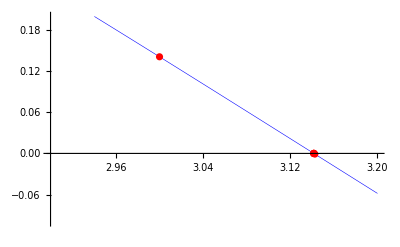

```mathematica
Show[
Plot[g[x],{x,2.9,3.2},PlotRange->{{2.9,3.2},{-0.1,0.2}},PlotStyle->{Thickness[0.001],Blue}],
ListPlot[{{x0,x1,x2,x3,x4,x5,x6},{g[x0],g[x1],g[x2],g[x3],g[x4],g[x5],g[x6]}}ᵀ,PlotStyle->Red]]
```

The convergence is so fast that we can only see the first few estimates as different from the exact value of π on this plot.